## Lab Report Sheet: Calculating Bond Densities

Arav Bhardwaj

## Data Collection: Determination of Maximum Electron Density

```mathematica
electrondensitydataCC = ({{"Compound", "Max e^- 
density 
(e^-/bohr^3)", "Bond
Length (Å)"}, {"C-C", 0.237, 1.543}, {"C=C", 0.361, 1.315}, {"C≡C", 0.410, 1.188}});
electrondensitydataCN= ({{"Compound", "Max e^- 
density 
(e^-/bohr^3)", "Bond
Length (Å)"}, {"C-N", 0.264, 1.472}, {"C=N", 0.401, 1.256}, {"C≡N", 0.499, 1.137}});
electrondensitydataNN = ({{"Compound", "Max e^- 
density 
(e^-/bohr^3)", "Bond
Length (Å)"}, {"N-N", 0.299, 1.450}, {"N=N", 0.500, 1.234}, {"N≡N", 0.696, 1.083}});
```

## Data Analysis: Determination of Maximum Electron Density

In the step below, I delete Row 1 (the header row), because I don't need to do any math with the header:

```mathematica
electrondensitydataCC = Delete[electrondensitydataCC,1];
electrondensitydataCN = Delete[electrondensitydataCN,1];
electrondensitydataNN = Delete[electrondensitydataNN,1];
```

In the step below, I put the data in column 1 into a variable called "compound", the data in column 2 into a variable called "density", and the data in column 3 into a variable called "length":

```mathematica
{compoundCC, densityCC, lengthCC} = Transpose[electrondensitydataCC];
{compoundCN, densityCN, lengthCN} = Transpose[electrondensitydataCN];
{compoundNN, densityNN, lengthNN} = Transpose[electrondensitydataNN];
```

In the step below, I join density and length into one dataset called "datafit".  Density is x, and length is y:

```mathematica
datafitCC=Transpose[{densityCC,lengthCC}];
datafitCN=Transpose[{densityCN,lengthCN}];
datafitNN=Transpose[{densityNN,lengthNN}];
```

Just for fun, I plot the datafit data to see what the line looks like:

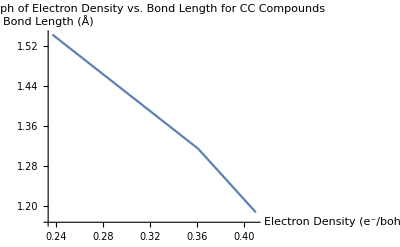

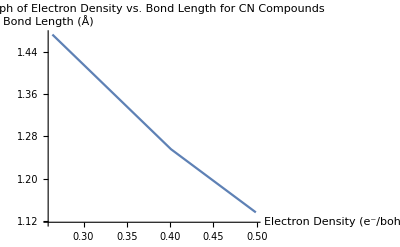

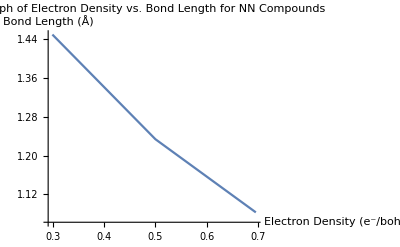

```mathematica
ccplot = ListLinePlot[datafitCC, PlotLabel -> "Graph of Electron Density vs. Bond Length for CC Compounds", AxesLabel -> {"Electron Density (e^-/bohr^3)", "Bond Length (Å)"}]
cnplot = ListLinePlot[datafitCN,PlotLabel -> "Graph of Electron Density vs. Bond Length for CN Compounds", AxesLabel -> {"Electron Density (e^-/bohr^3)", "Bond Length (Å)"}]
nnplot = ListLinePlot[datafitNN,PlotLabel -> "Graph of Electron Density vs. Bond Length for NN Compounds", AxesLabel -> {"Electron Density (e^-/bohr^3)", "Bond Length (Å)"}]
```

In the step below, I create a "y=mx+b" plot using LinearModelFit.  The two x's say to give me a y=mx+b fit.  The Normal command displays the results in a relatively familiar form (although it's y = b +mx form!):

```mathematica
fitCC=LinearModelFit[datafitCC,x,x]
Normal[fitCC]
fitCN=LinearModelFit[datafitCN,x,x]
Normal[fitCN]
fitNN=LinearModelFit[datafitNN,x,x]
Normal[fitCC]
```

FittedModel[2.02417-2.01044 x]

2.02417-2.01044 x

FittedModel[1.84519-1.43519 x]

1.84519-1.43519 x

FittedModel[1.71666-0.925072 x]

2.02417-2.01044 x

## Data Collection: Determining Electron Density at a Specific Value

specificdensitydata = ("Compound" | "e^- 
density 
(e^-/bohr^3)" | "Amount seen
(qualitative
description"
"C-C" | 0.3 | None
"C=C" | 0.3 | More
"C≡C" | 0.3 | A lot
"C-N" | 0.4 | None
"C=N" | 0.4 | A little
"C≡N" | 0.4 | A lot 
"N-N" | 0.5 | None
"N=N" | 0.5 | A little
"N≡N" | 0.5 | A lot )

Question:  what do you think these results mean?

These results show that electron density increases as the number of bonds between two atoms increases. This is because the distance between the two atoms decreases, and the quantity of electrons in the space increases (“bonds” are really just pair of electrons, so increasing the number of bonds increases the number of electrons).  According to the graph, this can be approximated as a linear relationship. This could also be observed qualitatively as the electron clouds grew larger at the same electron densities as the number of bonds grew.